```mathematica
IDM
```

{0.982309,0.738764,0.469125,0.197272,-0.060906,-0.304288,-0.544641,-0.798691,-1.07703,-1.36945,-1.62953,-1.77797,-1.75361,-1.5693,-1.24932,-0.780287,-0.360838,-0.0524176,0.,0.0301224,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,11.4912,23.8428,36.7985,50.0873,63.4443,76.6188,89.3687,101.447,112.587,122.505,130.922,137.636,142.584,145.871,147.749,148.611,148.903,148.989,148.99,149.005,149.005,149.005,149.005,149.005,149.005,149.005,149.005,149.005,149.005,149.005}

{11.,11.9823,12.7211,13.1902,13.3875,13.3266,13.0223,12.4776,11.6789,10.6019,9.23247,7.60294,5.82498,4.07137,2.50206,1.25274,0.472457,0.111619,0.0592013,0.,0.0301224,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

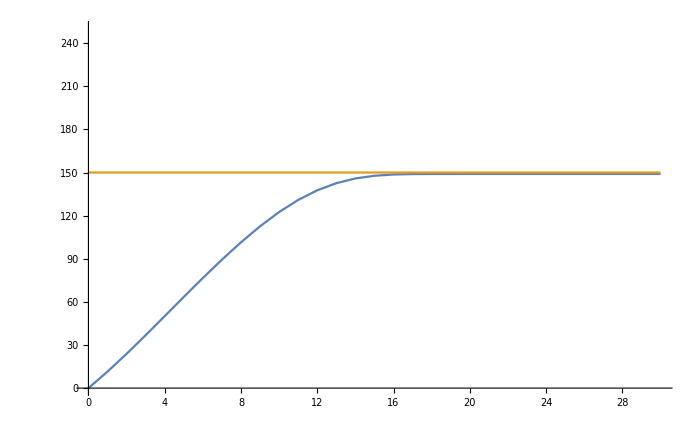

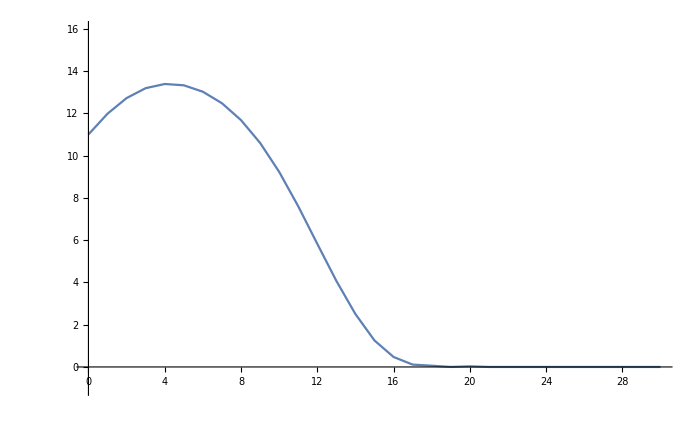

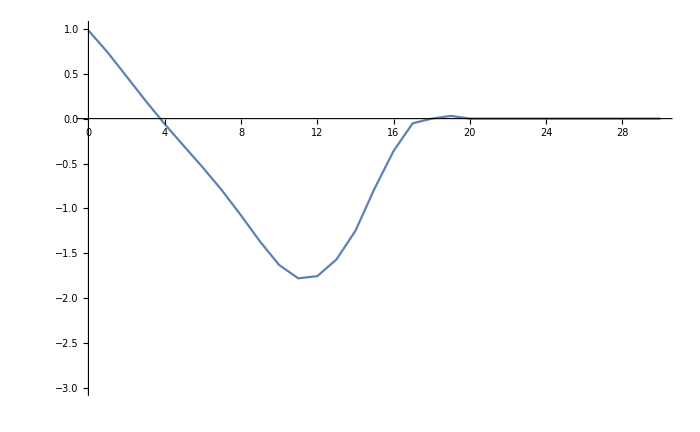

```mathematica
Clear["Global`*"]

s0=1.0;
T=1.0;
aMax=1.5;
b=1.5;
d=4;
v0=16.0;
dt=1.0;
K=30/dt;
x=Table[-1,{i,1,K+1}];v=Table[-1,{i,1,K+1}];u=Table[0.0,{i,1,K+1}];
xobs=Table[-1,{i,1,K+1}];vobs=Table[-1,{i,1,K+1}];
tls=Table[1,{i,1,K+1}];

s[x_,xobs_]:=x-xobs
sStar[v_,vl_]:=s0+Max[v*T+((v*(v-vl))/(2.0*Sqrt[aMax*b])),0.0]

aFree[v_]:=aMax*(1.0-(v/v0)^d)
aIDM[v_,vl_,x_,xobs_,I_]:=aFree[v]-I*(aMax*(sStar[v,vl]/(s[x,xobs]))^2)
(*aIDM[v_,vl_,x_,xobs_,I_]:=Min[aFree[v],(aMax*(sStar[v,vl]/(s[x,xobs]))^2)]*)

(*For[k=25/dt,k<=K,k++,tls[[k]]=0];*)

xobs[[1]]=150.0;vobs=0.0;
x[[1]]=0.0;v[[1]]=11.0;
For[k=1,k<=K,k++,
u[[k]]=aIDM[v[[k]],vobs,x[[k]],xobs[[k]],tls[[k]]];
x[[k+1]]=x[[k]]+v[[k]]*dt+0.5*u[[k]]*dt^2;
v[[k+1]]=v[[k]]+u[[k]]*dt;
If[v[[k+1]]<=0.0 ,
u[[k]]=0.0;(*aCon=(v[[k]]+0.1)/dt;*)aCon=b;
x[[k+1]]=x[[k]]+v[[k]]^2/(2.0*aCon);
v[[k+1]]=0.0;
];
xobs[[k+1]]=xobs[[k]];
]

Print[u];Print[x];Print[v];
ts=Table[(k-1)*dt,{k,1,K+1}];tsa=Table[(k-1)*dt,{k,1,K}];
xData=TemporalData[{x,xobs},{ts}];vData=TemporalData[{v},{ts}];aData=TemporalData[{u},{ts}];
ListLinePlot[xData,PlotRange->{{0,K*dt},{0,xobs[[1]]+100}}, ImageSize->700]
ListLinePlot[vData,PlotRange->{{0,K*dt},{-1,v0}}, ImageSize->700]
ListLinePlot[aData,PlotRange->{{0,K*dt},{-3,1}}, ImageSize->700]
```

```mathematica
ARRB Model
```

```mathematica
m=1600.0;alpha=0.666;beta1=0.0717;beta2=0.0344;b1=0.269;b2=0.0171;b3=0.000672;

Rt[v_,a_]:=b1+b2*v^2+b3*v^2+m*a/1000.0

fuel=0.0;
For[k=1,k<=K+1,k++,
vk=v[[k]];ak=u[[k]];
If[Rt[vk,ak]>0.0,
If[ak>0.0,
fuel+=alpha+beta1*Rt[vk,ak]*vk+(beta2*m*ak^2*vk/1000.0),
fuel+=alpha+beta1*Rt[vk,ak]*vk
],
fuel+=alpha;
]
]
fuel*dt
StringForm["Fuel Consumption: `1`",NumberForm[fuel*dt,{7,5}]]
```

46.1161

Fuel Consumption: 46.11607

```mathematica
MOBIL
```

```mathematica
(* IDM function -> aIDM(...) *)

For[k=1,k<=K,k++,



]
```